```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["../lib/lib2.m"];
Get["../lib/util.m"];
```

```mathematica
data = Import["../../runs/Trials/last.dat"];
```

```mathematica
changeNK[9, 9];
```

```mathematica
cmatdata = cMatOne/@data;
```

```mathematica
eig = Flatten[Eigenvalues/@Flatten[cmatdata[[All, 2;;]], 1]];
```

```mathematica
eig//Length
```

29160

```mathematica
xel = Join[
Flatten@Table[($N)/(√($N-1)) cmatdata[[All, 2;;, a, a]]//Chop, {a, 1, $N}],
Flatten@Table[√(2$N)ReIm@cmatdata[[All, 2;;, a, b]]//Chop, {a, 1, $N}, {b, a+1, $N}]
];
```

```mathematica
Mean[Flatten@Table[√(2$N)ReIm@cmatdata[[All, 2;;, a, b]]//Chop, {a, 1, $N}, {b, a+1, $N}]]
```

0.0000428004

```mathematica
FindDistribution[Flatten@Table[($N)/(√($N-1)) cmatdata[[All, 2;;, a, a]]//Chop, {a, 1, $N}]]
```

NormalDistribution[0.00024429,0.190957]

```mathematica
FindDistribution[xel]
```

NormalDistribution[0.00899546,0.188731]

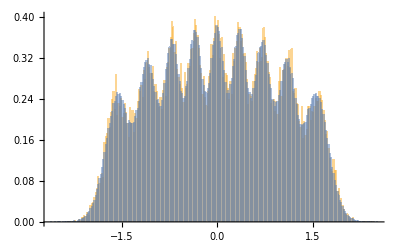

```mathematica
Histogram[{Standardize[eig], Standardize[randEig]}, 300, PDF]
```

```mathematica
randEig = Flatten[Eigenvalues/@((# - 1/($N)Tr[#]IdentityMatrix[$N])&/@RandomVariate[GaussianUnitaryMatrixDistribution[1/(√($N)), $N], 100000])];
```